# Index of Conicidence

## References

http://www.murky.org/blg/2004/10/index-of-coincidences-a-worked-example/

http://en.wikipedia.org/wiki/Index_of_coincidence

http://practicalcryptography.com/cryptanalysis/text-characterisation/index-coincidence/

## Conincidence Table & Plot (kappaIC)

```mathematica
testText = DeleteCases[Characters["QPWKA LVRXC QZIKG RBPFA EOMFL  JMSDZ VDHXC XJYEB IMTRQ WNMEA
IZRVK CVKVL XNEIC FZPZC ZZHKM  LVZVZ IZRRQ WDKEC HOSNY XXLSP
MYKVQ XJTDC IOMEE XDQVS RXLRL  KZHOV"]," "]
```

{Q,P,W,K,A,L,V,R,X,C,Q,Z,I,K,G,R,B,P,F,A,E,O,M,F,L,J,M,S,D,Z,V,D,H,X,C,X,J,Y,E,B,I,M,T,R,Q,W,N,M,E,A,
,I,Z,R,V,K,C,V,K,V,L,X,N,E,I,C,F,Z,P,Z,C,Z,Z,H,K,M,L,V,Z,V,Z,I,Z,R,R,Q,W,D,K,E,C,H,O,S,N,Y,X,X,L,S,P,
,M,Y,K,V,Q,X,J,T,D,C,I,O,M,E,E,X,D,Q,V,S,R,X,L,R,L,K,Z,H,O,V}

```mathematica
testTextShifted=RotateRight[testText,1]
```

{V,Q,P,W,K,A,L,V,R,X,C,Q,Z,I,K,G,R,B,P,F,A,E,O,M,F,L,J,M,S,D,Z,V,D,H,X,C,X,J,Y,E,B,I,M,T,R,Q,W,N,M,E,A,
,I,Z,R,V,K,C,V,K,V,L,X,N,E,I,C,F,Z,P,Z,C,Z,Z,H,K,M,L,V,Z,V,Z,I,Z,R,R,Q,W,D,K,E,C,H,O,S,N,Y,X,X,L,S,P,
,M,Y,K,V,Q,X,J,T,D,C,I,O,M,E,E,X,D,Q,V,S,R,X,L,R,L,K,Z,H,O}

```mathematica
kappaIC[text_,shift_,c_:26]:= Module[{textL=Select[Characters[ToUpperCase[text]],LetterQ]},Divide[Sum[If[textL[[i]]==textL[[Mod[i+shift,Length[textL]]]], 1, 0],{i,1,Length[textL]}],(Length[textL]/c)]]
```

```mathematica
testText = "QPWKA LVRXC QZIKG RBPFA EOMFL  JMSDZ VDHXC XJYEB IMTRQ WNMEA
IZRVK CVKVL XNEIC FZPZC ZZHKM  LVZVZ IZRRQ WDKEC HOSNY XXLSP
MYKVQ XJTDC IOMEE XDQVS RXLRL  KZHOV";
```

```mathematica
kappaIC[testText,1]
```

4+If[O==List,1,0]

```mathematica
RotateRight[{a,b,c,d,e},2][[2]]
```

e

```mathematica
kappaIC[text_,shift_,c_:26]:= Module[{textL=Select[Characters[ToUpperCase[text]],LetterQ]},Divide[Sum[If[textL[[i]]==RotateRight[textL,shift][[i]], 1, 0],{i,1,Length[textL]}],(Length[textL]/c)]]
```

```mathematica
kappaIC[testText,1]
```

4+If[O==List,1,0]

```mathematica
Clear[kappaIC]
```

```mathematica
kappaIC[text_,shift_,c_:26]:= Module[{textL=Select[Characters[ToUpperCase[text]],LetterQ]},Divide[Sum[If[textL[[i]]==RotateRight[textL,shift][[i]], 1, 0],{i,1,Length[textL]}],(Length[textL]/c)]] //N
```

```mathematica
kappaIC[testText,1]
```

0.8

```mathematica
kappaICTable[text_,maxShifts_,c_:26]:=ParallelTable[{shift, kappaIC[text,shift,c]},{shift,1,maxShifts}] //TableForm
```

```mathematica
kappaICTable[testText, 15]
```

1 | 0.8
2 | 1.6
3 | 1.
4 | 0.6
5 | 0.8
6 | 0.8
7 | 0.6
8 | 0.8
9 | 1.
10 | 1.4
11 | 1.2
12 | 0.2
13 | 1.2
14 | 0.8
15 | 1.6

```mathematica
kappaICPlot[text_,maxShifts_,c_:26]:=Plot[kappaIC[text,shift,c],{shift,1,maxShifts}]
```

```mathematica
kappaICPlot[testText,15]
```

RotateRight::rspec: Rotation specification {1.00029} should be a machine-sized integer or list of machine-sized integers.

General::stop: Further output of RotateRight :: rspec will be suppressed during this calculation.

Part::partw: Part 3 of RotateRight[{"Q", "P", "W", "K", "A", "L", "V", "R", "X", "C", "Q", "Z", "I", "K", "G", "R", "B", "P", "F", "A", "E", "O", "M", "F", "L", "J", "M", "S", "D", "Z", "V", "D", "H", "X", "C", "X", "J", "Y", "E", "B", "I", "M", "T", "R", "Q", "W", "N", "M", "E", "A", « 80 »}, 1.00029] does not exist.

Part::partw: Part 4 of RotateRight[{"Q", "P", "W", "K", "A", "L", "V", "R", "X", "C", "Q", "Z", "I", "K", "G", "R", "B", "P", "F", "A", "E", "O", "M", "F", "L", "J", "M", "S", "D", "Z", "V", "D", "H", "X", "C", "X", "J", "Y", "E", "B", "I", "M", "T", "R", "Q", "W", "N", "M", "E", "A", « 80 »}, 1.00029] does not exist.

Part::partw: Part 5 of RotateRight[{"Q", "P", "W", "K", "A", "L", "V", "R", "X", "C", "Q", "Z", "I", "K", "G", "R", "B", "P", "F", "A", "E", "O", "M", "F", "L", "J", "M", "S", "D", "Z", "V", "D", "H", "X", "C", "X", "J", "Y", "E", "B", "I", "M", "T", "R", "Q", "W", "N", "M", "E", "A", « 80 »}, 1.00029] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

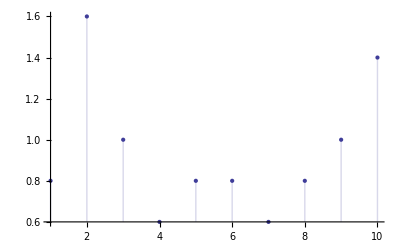

```mathematica
DiscretePlot[kappaIC[testText,i],{i,1,10}]
```

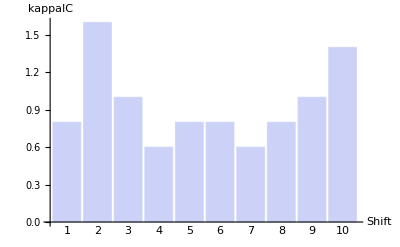

```mathematica
BarChart[ParallelTable[kappaIC[testText,i],{i,1,10}],{ChartLabels->Placed[Range[1,10],Below],AxesLabel->{"Shift","kappaIC"}}]
```

```mathematica
kappaICPlot[text_,maxShifts_,c_:26]:=BarChart[ParallelTable[kappaIC[text,i,c],{i,1,maxShifts}],{ChartLabels->Placed[Range[1,maxShifts],Below],AxesLabel->{"Shift","kappaIC"}}]
```

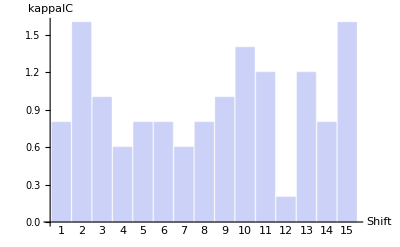

```mathematica
kappaICPlot[testText,15]
```